```mathematica
ppRawData={pLabInv[m0@N938,m0@N938,First[#]],Second[#]}&/@{{0.14000,314.00},{0.19000,155.00},{0.24000,92.000},{0.28000,70.000},{0.31000,52.800},{0.35000,42.500},{0.37000,37.400},{0.39000,33.900},{0.43000,28.500},{0.44000,27.700},{0.49000,24.800},{0.54000,25.200},{0.57000,26.100},{0.59000,23.200},{0.60658,24.200},{0.60700,24.550},{0.65847,25.800},{0.69000,22.400},{0.72000,22.400},{0.75000,22.600},{0.75700,23.850},{0.75732,23.850},{0.83000,24.300},{0.83086,24.300},{0.84600,24.400},{0.85000,23.400},{0.87179,24.550},{0.87200,24.450},{0.88000,23.200},{0.93000,24.400},{0.93700,25.650},{0.93736,25.700},{0.96300,26.300},{0.96336,26.500},{0.96545,24.000},{0.96824,26.500},{0.99452,24.200},{1.00000,28.000},{1.00549,23.800},{1.00891,27.950},{1.00900,27.750},{1.00959,27.000},{1.03673,28.000},{1.09008,29.900},{1.09300,30.950},{1.09337,31.250},{1.10783,31.950},{1.10800,31.650},{1.11100,32.900},{1.12700,30.000},{1.13586,29.800},{1.14234,32.100},{1.16168,34.800},{1.16200,34.500},{1.19365,35.600},{1.20634,36.000},{1.21500,39.000},{1.21898,36.600},{1.23786,37.700},{1.24413,38.600},{1.26909,39.800},{1.28140,41.800},{1.28900,43.234},{1.29017,41.000},{1.29388,41.400},{1.32300,43.000},{1.39149,44.400},{1.40800,46.487},{1.42000,46.200},{1.42400,46.000},{1.46329,47.000},{1.49881,47.800},{1.52235,47.600},{1.53100,47.400},{1.54580,47.940},{1.59240,46.100},{1.60000,47.500},{1.60700,47.476},{1.62800,49.000},{1.66000,47.553},{1.68700,48.000},{1.69604,47.400},{1.73000,46.200},{1.78000,47.490},{1.78127,48.300},{1.78500,47.000},{1.85800,47.455},{1.88600,47.400},{1.89000,46.800},{1.94000,47.357},{1.95200,47.409},{1.99000,47.000},{2.00455,47.500},{2.02661,49.400},{2.05000,45.300},{2.07900,47.224},{2.21200,46.985},{2.23968,47.200},{2.28000,46.669},{2.41900,46.130},{2.45000,45.827},{2.47000,45.100},{2.59200,45.533},{2.68000,45.331},{2.70400,45.174},{2.78444,41.400},{2.81900,45.008},{2.85700,44.928},{2.88976,45.540},{2.95800,44.651},{2.97000,44.500},{2.99400,44.466},{3.05400,44.401},{3.11000,44.188},{3.13100,44.156},{3.14200,44.114},{3.27000,47.100},{3.27700,43.610},{3.30300,43.669},{3.41160,41.600},{3.44400,43.138},{3.54600,42.978},{3.58000,43.200},{3.67024,42.100},{3.73100,42.680},{3.90800,42.316},{4.00000,42.200},{4.03700,42.136},{4.15000,39.700},{4.20000,42.200},{4.26500,41.765},{4.50990,42.100},{4.55200,41.457},{4.78300,41.377},{4.96600,41.165}};
pnRawData={pLabInv[m0@N938,m0@N938,First[#]],Second[#]}&/@
{
{0.05311,3447.},{0.061,2907.2},{0.06907,2536.},{0.07633,2274.},{0.084,1945.4},{0.091,1744.4},{0.098,1577.3},{0.106,1402.},{0.115,1238.1},{0.12287,1134.},{0.13047,1026.},{0.14,892.87},{0.147,820.73},{0.155,745.52},{0.162,686.08},{0.167,650.32},{0.173,608.56},{0.178,597.},{0.18375,560.},{0.189,513.93},{0.19324,495.},{0.198,470.06},{0.204,420.},{0.20923,411.},{0.216,393.4},{0.221,373.55},{0.227,354.29},{0.23234,340.},{0.238,320.45},{0.245,297.2},{0.255,260.1},{0.27707,170.},{0.301,170.3},{0.331,141.5},{0.35858,114.9},{0.403,85.3},{0.42826,80.316},{0.447,71.5},{0.47667,65.355},{0.51524,57.021},{0.5576,50.768},{0.59209,46.318},{0.64131,42.022},{0.725,42.8},{0.80854,34.563},{0.9108,35.05},{0.98267,32.548},{1.08407,35.15},{1.18153,34.662},{1.275,36.85},{1.375,37.85},
{1.40700,39.440},{1.59240,39.200},{1.60700,39.770},{1.65900,40.090},{1.77900,40.559},{1.85700,41.224},{1.94000,41.530},{1.95200,41.479},{2.07800,41.905},{2.21200,42.174},{2.28000,42.500},{2.44900,42.684},{2.59200,42.890},{2.68000,42.961},{2.70400,42.933},{2.81900,43.017},{2.85700,43.037},{2.95700,43.113},{2.99300,43.115},{3.05400,42.979},{3.10900,43.226},{3.14200,43.118},{3.44400,42.582},{3.54600,42.522},{3.90700,42.525},{4.03600,42.495},{4.26400,42.276},{4.96500,42.069},{5.22000,42.017},{5.52600,42.034},{5.82400,41.821}
};
```

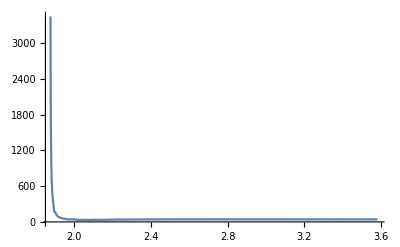

```mathematica
ListLinePlot[pnRawData,PlotRange->All]
```

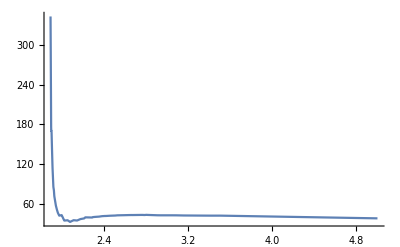

```mathematica
Plot[Interpolation[pnRawData,x,InterpolationOrder->1],{x,1.89,5},PlotRange->{0,All}]
```

```mathematica
pnRawData
```

{{1.87675,3447.},{1.87699,2907.2},{1.87727,2536.},{1.87755,2274.},{1.87788,1945.4},{1.8782,1744.4},{1.87855,1577.3},{1.87898,1402.},{1.87951,1238.1},{1.88,1134.},{1.88051,1026.},{1.88119,892.87},{1.88172,820.73},{1.88235,745.52},{1.88293,686.08},{1.88336,650.32},{1.88389,608.56},{1.88435,597.},{1.88489,560.},{1.8854,513.93},{1.88582,495.},{1.88631,470.06},{1.88693,420.},{1.88749,411.},{1.88823,393.4},{1.8888,373.55},{1.88949,354.29},{1.89012,340.},{1.8908,320.45},{1.89167,297.2},{1.89295,260.1},{1.89593,170.},{1.89941,170.3},{1.90413,141.5},{1.90881,114.9},{1.91701,85.3},{1.92201,80.316},{1.92587,71.5},{1.93224,65.355},{1.94097,57.021},{1.95111,50.768},{1.95975,46.318},{1.97265,42.022},{1.99593,42.8},{2.02062,34.563},{2.05242,35.05},{2.07562,32.548},{2.10927,35.15},{2.14238,34.662},{2.17466,36.85},{2.20958,37.85},{2.22081,39.44},{2.28621,39.2},{2.29138,39.77},{2.30976,40.09},{2.35215,40.559},{2.37963,41.224},{2.40878,41.53},{2.41298,41.479},{2.45698,41.905},{2.50341,42.174},{2.52682,42.5},{2.58447,42.684},{2.63266,42.89},{2.66203,42.961},{2.67001,42.933},{2.70799,43.017},{2.72046,43.037},{2.75308,43.113},{2.76475,43.115},{2.78445,42.979},{2.80211,43.226},{2.81267,43.118},{2.90792,42.582},{2.93952,42.522},{3.04918,42.525},{3.08756,42.495},{3.1544,42.276},{3.35243,42.069},{3.42188,42.017},{3.50353,42.034},{3.58138,41.821}}

InterpolatingFunction::dmval: Input value {1.88} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.26} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.28} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

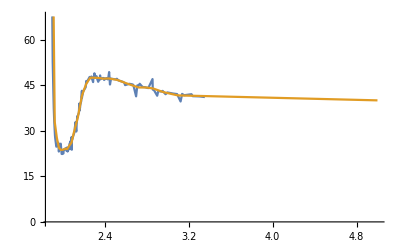

```mathematica
ppData=
{{1.88119,314.00}}~Join~
Table[{Mean[First/@rs],Mean[Second/@rs]},
{rs,
inGroupsOf[5][ppRawData]
}];
ppEvenData=Table[{eCM,Interpolation[ppData,eCM,InterpolationOrder->1]},{eCM,1.88,5.0,0.02}];
ListLinePlot[{ppRawData,ppEvenData}]
```

InterpolatingFunction::dmval: Input value {3.56} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.58} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

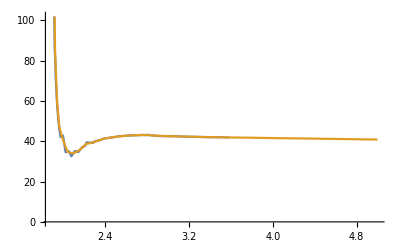

```mathematica
pnData=
{{1.8767510263842062,3447.}}~Join~
Table[{Mean[First/@rs],Mean[Second/@rs]},
{rs,
inGroupsOf[2][pnRawData]
}];
pnEvenData=Table[{eCM,Interpolation[pnData,eCM,InterpolationOrder->1]},{eCM,1.88,5.0,0.02}];
ListLinePlot[{pnRawData,pnEvenData}]
```

```mathematica
Second/@pnEvenData
```

{1135.35,170.185,84.5462,58.9083,47.5717,43.3222,40.1235,37.2117,34.7469,34.4045,34.0621,34.067,34.6442,35.2214,35.8313,36.8508,37.8704,38.6998,38.9281,39.1564,39.3846,39.7081,40.1064,40.475,40.8079,41.1407,41.4218,41.5763,41.7324,41.8934,42.0543,42.2153,42.3605,42.4568,42.5531,42.6495,42.7458,42.8188,42.8745,42.9302,42.9702,43.0034,43.0382,43.0772,43.1136,43.1069,43.0772,43.0018,42.9265,42.8511,42.802,42.7533,42.7046,42.6559,42.6072,42.5585,42.5173,42.4955,42.4738,42.452,42.4302,42.4084,42.3866,42.361,42.3353,42.3096,42.2838,42.2581,42.2323,42.2066,42.1809,42.1551,42.1294,42.1037,42.0779,42.0522,42.0334,42.0186,42.0037,41.9888,41.974,41.9591,41.9442,41.9293,41.9145,41.8996,41.8847,41.8698,41.855,41.8401,41.8252,41.8103,41.7955,41.7806,41.7657,41.7508,41.736,41.7211,41.7062,41.6913,41.6765,41.6616,41.6467,41.6318,41.617,41.6021,41.5872,41.5724,41.5575,41.5426,41.5277,41.5129,41.498,41.4831,41.4682,41.4534,41.4385,41.4236,41.4087,41.3939,41.379,41.3641,41.3492,41.3344,41.3195,41.3046,41.2897,41.2749,41.26,41.2451,41.2302,41.2154,41.2005,41.1856,41.1708,41.1559,41.141,41.1261,41.1113,41.0964,41.0815,41.0666,41.0518,41.0369,41.022,41.0071,40.9923,40.9774,40.9625,40.9476,40.9328,40.9179,40.903,40.8881,40.8733,40.8584,40.8435}

```mathematica
pnRawData
```

{{1.87675,3447.},{1.87699,2907.2},{1.87727,2536.},{1.87755,2274.},{1.87788,1945.4},{1.8782,1744.4},{1.87855,1577.3},{1.87898,1402.},{1.87951,1238.1},{1.88,1134.},{1.88051,1026.},{1.88119,892.87},{1.88172,820.73},{1.88235,745.52},{1.88293,686.08},{1.88336,650.32},{1.88389,608.56},{1.88435,597.},{1.88489,560.},{1.8854,513.93},{1.88582,495.},{1.88631,470.06},{1.88693,420.},{1.88749,411.},{1.88823,393.4},{1.8888,373.55},{1.88949,354.29},{1.89012,340.},{1.8908,320.45},{1.89167,297.2},{1.89295,260.1},{1.89593,170.},{1.89941,170.3},{1.90413,141.5},{1.90881,114.9},{1.91701,85.3},{1.92201,80.316},{1.92587,71.5},{1.93224,65.355},{1.94097,57.021},{1.95111,50.768},{1.95975,46.318},{1.97265,42.022},{1.99593,42.8},{2.02062,34.563},{2.05242,35.05},{2.07562,32.548},{2.10927,35.15},{2.14238,34.662},{2.17466,36.85},{2.20958,37.85},{2.22081,39.44},{2.28621,39.2},{2.29138,39.77},{2.30976,40.09},{2.35215,40.559},{2.37963,41.224},{2.40878,41.53},{2.41298,41.479},{2.45698,41.905},{2.50341,42.174},{2.52682,42.5},{2.58447,42.684},{2.63266,42.89},{2.66203,42.961},{2.67001,42.933},{2.70799,43.017},{2.72046,43.037},{2.75308,43.113},{2.76475,43.115},{2.78445,42.979},{2.80211,43.226},{2.81267,43.118},{2.90792,42.582},{2.93952,42.522},{3.04918,42.525},{3.08756,42.495},{3.1544,42.276},{3.35243,42.069},{3.42188,42.017},{3.50353,42.034},{3.58138,41.821}}

```mathematica
Second/@ppEvenData
```

{335.561,99.5353,32.9358,27.753,24.4147,23.7205,23.8078,24.1367,24.0177,25.2023,26.1183,29.1103,31.7825,34.3526,38.1058,41.6417,43.6273,45.439,46.5519,47.5467,47.5348,47.5201,47.4971,47.4584,47.3441,47.2299,47.2413,47.2926,47.2723,47.1574,47.0425,46.9276,46.7771,46.5213,46.2655,46.0097,45.7539,45.4981,45.2562,45.0241,44.792,44.5599,44.3278,44.3162,44.3281,44.34,44.2698,44.1811,44.0924,43.9772,43.7315,43.4857,43.24,42.9942,42.7736,42.6152,42.4568,42.2983,42.1399,41.9815,41.8231,41.7054,41.6882,41.6711,41.6539,41.6367,41.6195,41.6023,41.5851,41.5679,41.5507,41.5335,41.5164,41.4992,41.482,41.4648,41.4476,41.4304,41.4132,41.396,41.3788,41.3617,41.3445,41.3273,41.3101,41.2929,41.2757,41.2585,41.2413,41.2241,41.207,41.1898,41.1726,41.1554,41.1382,41.121,41.1038,41.0866,41.0694,41.0522,41.0351,41.0179,41.0007,40.9835,40.9663,40.9491,40.9319,40.9147,40.8975,40.8804,40.8632,40.846,40.8288,40.8116,40.7944,40.7772,40.76,40.7428,40.7257,40.7085,40.6913,40.6741,40.6569,40.6397,40.6225,40.6053,40.5881,40.571,40.5538,40.5366,40.5194,40.5022,40.485,40.4678,40.4506,40.4334,40.4162,40.3991,40.3819,40.3647,40.3475,40.3303,40.3131,40.2959,40.2787,40.2615,40.2444,40.2272,40.21,40.1928,40.1756,40.1584,40.1412,40.124,40.1068,40.0897,40.0725}